```mathematica
NodeTypes={"Input","Hidden","Output","Bias"};
ActivationFunction ={"Sine","Abs","Id","Mod","Gaus"};
ActivationIcons ={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
setColor[symbol_,color_]:=ColorReplace[symbol,DominantColors[symbol]⟦3⟧->color,0.01];
```

```mathematica
GetPathFromNo[orgNo_]:= StringForm["D:\\betterOutput\\organisms\\org``.json",orgNo]//ToString;
GetOrganism[path_]:=
Quiet[
{
"genome",
"nervesystem",
"parent"
}/.Import[path]
]
DrawGenome[path_]:=Module[{g,n,p,vertices,vertexInfo,vertexStyle,vertexShape,vertexShape2,edges,weights},
{g,n,p}=GetOrganism[path];
vertices="i"/.("vertices"/.g);
vertexInfo="i"->Tooltip["i",StringForm["i: ``\ntype: ``\nf: ``.","i",NodeTypes⟦"type"+1⟧//Quiet,ActivationFunction⟦"f"+1⟧//Quiet]]/.("vertices"/.g);
vertexStyle=("i"->{"type"}/.("vertices"/.g))/.{{0}->RGBColor[0.368627, 0.556863, 0.956863],{1}->RGBColor[0.72, 0.72, 0.72],{2}->RGBColor[0.72, 0.28, 0.32],{3}->RGBColor[0.92, 0.67, 0.32]};
vertexShape="i"->( ActivationIcons⟦"f"+1⟧//Quiet)/.("vertices"/.g);
edges = "i"->"o"/.("links"/.g);
weights=Round[#,0.01]&/@("w"/.("links"/.g));
vertexShape=Table[i->setColor[i/.vertexShape,i/.vertexStyle],{i,Keys[vertexStyle]}];
vertexShape2=Map[Cases[vertexShape,HoldPattern[#->_]]&,VertexList[Graph[edges]]]//Flatten;
g=Graph[
(*vertices,*)
edges,
EdgeWeight->weights,
VertexShape->vertexShape2,
VertexLabels->Placed["Name",Center],
VertexSize->1/2,
GraphLayout->"LayeredEmbedding",
ImageSize->Small,EdgeLabels->"EdgeWeight"
]
]
DrawNerveSystem[path_]:=Module[{g,n,p,vertices,vertexInfo,vertexStyle,vertexShape,vertexShape2,edges,weights},
{g,n,p}=GetOrganism[path];
vertices="i"/.("vertices"/.n);
vertexInfo="i"->Tooltip["i",StringForm["i: ``\ntype: ``\nf: ``.","i",NodeTypes⟦"type"+1⟧//Quiet,ActivationFunction⟦"f"+1⟧//Quiet]]/.("vertices"/.n);
vertexStyle=("i"->{"type"}/.("vertices"/.n))/.{{0}->RGBColor[0.368627, 0.556863, 0.956863],{1}->RGBColor[0.72, 0.72, 0.72],{2}->RGBColor[0.72, 0.28, 0.32],{3}->RGBColor[0.92, 0.67, 0.32]};
vertexShape="i"->( ActivationIcons⟦"f"+1⟧//Quiet)/.("vertices"/.n);
edges = "i"->"o"/.("links"/.n);
weights=Round[#,0.01]&/@("w"/.("links"/.n));
vertexShape=Table[i->setColor[i/.vertexShape,i/.vertexStyle],{i,Keys[vertexStyle]}];
vertexShape2=Map[Cases[vertexShape,HoldPattern[#->_]]&,VertexList[Graph[edges]]]//Flatten;
g=Graph[
(*vertices,*)
edges,
EdgeWeight->weights,
VertexShape->vertexShape2,
VertexLabels->Placed["Name",Center],
VertexSize->1/2,
GraphLayout->"LayeredEmbedding",
ImageSize->Small,EdgeLabels->"EdgeWeight"
]
]
```

```mathematica
dir=SystemDialogInput["FileOpen"]
```

D:\newLight3\organisms\org0.json

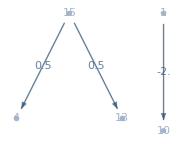

```mathematica
g=DrawGenome[dir]
```

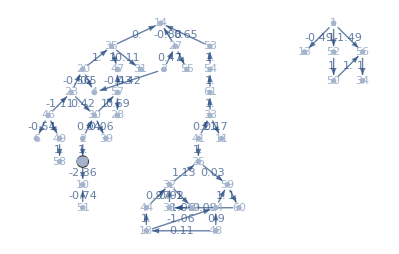

```mathematica
DrawGenome["D:\\newLight3\\organisms\\org628131.json"]
```

```mathematica
initorg=Labeled[Legended[g,Placed[SwatchLegend[{RGBColor[0.368627, 0.556863, 0.956863],RGBColor[0.72, 0.72, 0.72],RGBColor[0.72, 0.28, 0.32],RGBColor[0.92, 0.67, 0.32]},NodeTypes,LegendLayout->"Row"],Above]],"Genome"]
```

-Graphics-Genome

```mathematica
DisplayOrgGraphs[path_]:=
Legended[
Grid[{{
Labeled[DrawGenome[path],"Genome"],
Labeled[DrawNerveSystem[path],"Nervous system"]
}},
Dividers->Center,
FrameStyle->Gray
],
Placed[SwatchLegend[{RGBColor[0.368627, 0.556863, 0.956863],RGBColor[0.72, 0.72, 0.72],RGBColor[0.72, 0.28, 0.32],RGBColor[0.92, 0.67, 0.32]},
NodeTypes,
LegendLayout->"Row"
],
Above]
]
```

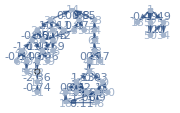
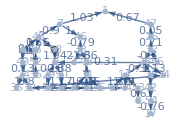
-Graphics-Genome | -Graphics-Nervous system

```mathematica
DisplayOrgGraphs["D:\\newLight3\\organisms\\org628131.json"]
```

```mathematica
{{"Genome", -Graphics-"Nervous system"}}
```

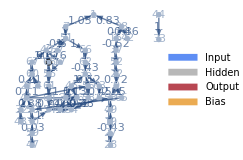
```mathematica
{{"Genome", -Graphics-"Nervous system"}}
```

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\repo\\grafiliv\\doc\\figs\\org0 genome.eps",initorg];
```

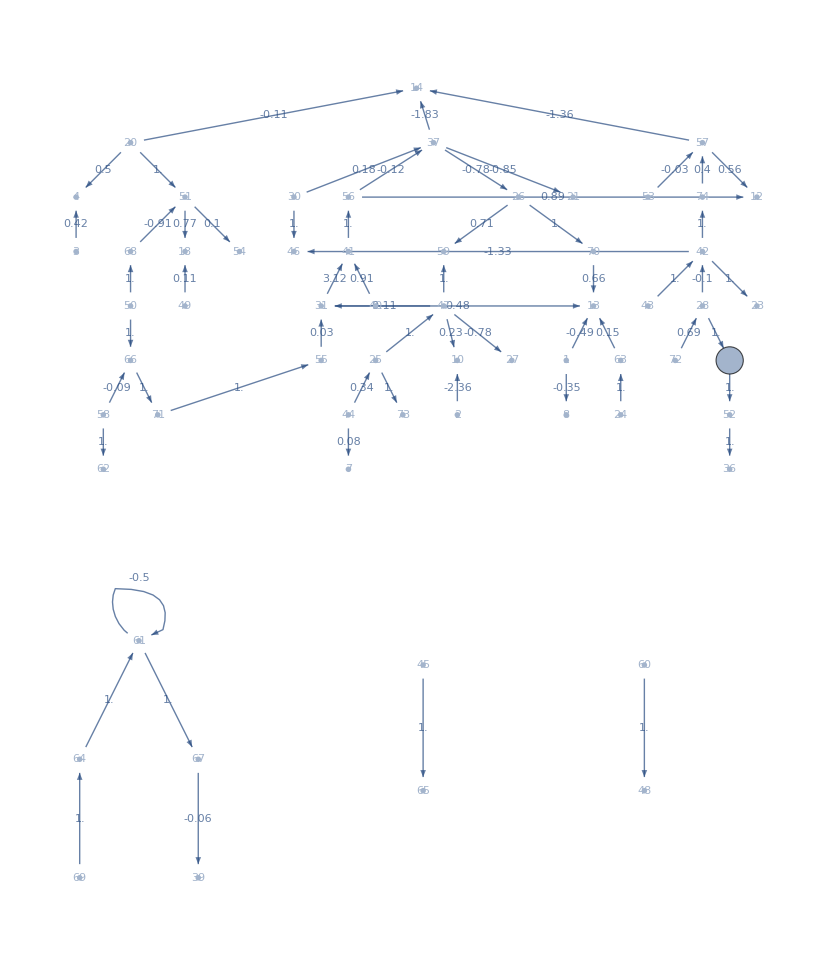

```mathematica
n=DrawGenome["D:\\newLight3\\organisms\\org632638.json"]
```

{7→1,27→28,30→34,38→16,19→27,26→39,40→17,32→41,41→26,43→32,44→33,37→16,39→46,46→36,41→21,19→49,22→9,48→39,30→50,50→41,7→51,38→42,22→52,52→37,40→51,49→53,34→54,54→39,9→53,41→55,55→36,17→56,51→57,55→58,46→26,38→1,47→59,59→30,4→60,56→61,34→53,62→36,8→54,36→63,63→8,21→60,61→64,64→34,9→65,65→50,51→66,66→62,60→67,67→40,56→68,68→40}

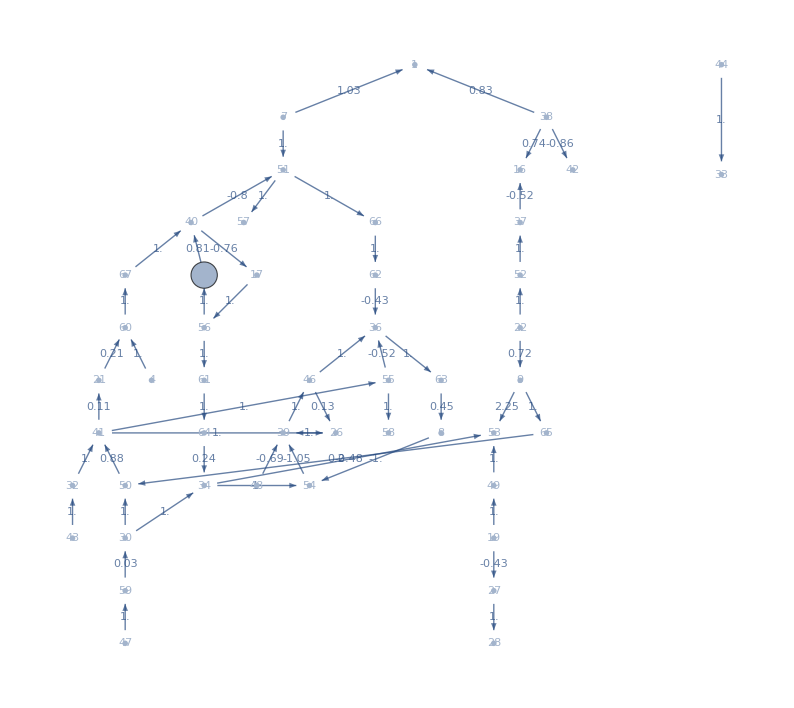

```mathematica
n=DrawNerveSystem["D:\\newLight3\\organisms\\org632638.json"]
```